```mathematica
Subscript[a, n]= Subscript[a, n-1]+Subscript[a, n-3]
```

a_(-3+n)+a_(-1+n)

LCM[8,n]

LCM[10,n]

Table::iterb: Iterator {i,0,n} does not have appropriate bounds.

Table::iterb: Iterator {i,0.,n} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListPlot::lpn: Table[formula[i],{i,0.,n}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Table[formula[i],{i,0,n}],Joined→True,Mesh→All,PlotStyle→color]

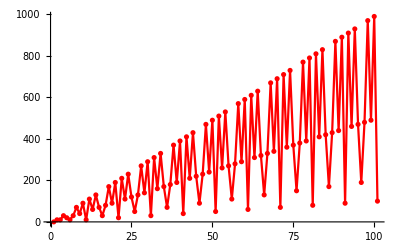

Show::gcomb: Could not combine the graphics objects in Show[plt1,].

Show[plt1,-Graphics-]

{1,2,3,4,6,9,13,19,28,41,60}

{2,3,4,6,9,13,19,28,41,60}

4

```mathematica
f[n_]:=f[n]=f[n-1]+f[n-3]
f[0]=1;
f[1]=2;
f[2]=3;
f1[n_]=LCM[n,8]
f2[n_]=LCM[n,10]
GraphSequence[formula_, n_Integer, color_:Blue]=
ListPlot[Table[formula[i],{i, 0, n}],Joined->True, Mesh->All, PlotStyle->color]
plt2=GraphSequence[f2, 100, Red]
Show[plt1, plt2]
Table[f[i], {i, 0, 10}]
Map[f, Range[10]]

f[3]
```

```mathematica
Subscript[a, 0]=1, Subscript[a, 1]=2, Subscript[a, 2]=3
```

```mathematica
GraphSequence[formula_, n_Integer, color_:Blue]=
ListPlot[Partition[Riffle[lst]],Joined->True, Mesh->All, PlotStyle->color]
```

```mathematica
Clear["Global`*"]
```

```mathematica
fArythm[n_]:=fArythm[n]=fArythm[n-1]+d
fArythm[0]=3;
d=5;
Table[fArythm[i],{i, 0, 50}]
```

{3,8,13,18,23,28,33,38,43,48,53,58,63,68,73,78,83,88,93,98,103,108,113,118,123,128,133,138,143,148,153,158,163,168,173,178,183,188,193,198,203,208,213,218,223,228,233,238,243,248,253}

```mathematica
fGeom[n_]:=fGeom[n]=fGeom[n-1]*q
fGeom[0]=1;
q=2;
Table[fGeom[i],{i, 0, 50}]
```

{1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768,65536,131072,262144,524288,1048576,2097152,4194304,8388608,16777216,33554432,67108864,134217728,268435456,536870912,1073741824,2147483648,4294967296,8589934592,17179869184,34359738368,68719476736,137438953472,274877906944,549755813888,1099511627776,2199023255552,4398046511104,8796093022208,17592186044416,35184372088832,70368744177664,140737488355328,281474976710656,562949953421312,1125899906842624}

```mathematica
fGeom2[n_]:=fGeom2[n]=fGeom2[n-1]*q
fGeom2[0]=1;
q=0.5;
Table[fGeom2[i],{i, 0, 50}]
```

{1,0.5,0.25,0.125,0.0625,0.03125,0.015625,0.0078125,0.00390625,0.00195313,0.000976563,0.000488281,0.000244141,0.00012207,0.0000610352,0.0000305176,0.0000152588,7.62939×10^-6,3.8147×10^-6,1.90735×10^-6,9.53674×10^-7,4.76837×10^-7,2.38419×10^-7,1.19209×10^-7,5.96046×10^-8,2.98023×10^-8,1.49012×10^-8,7.45058×10^-9,3.72529×10^-9,1.86265×10^-9,9.31323×10^-10,4.65661×10^-10,2.32831×10^-10,1.16415×10^-10,5.82077×10^-11,2.91038×10^-11,1.45519×10^-11,7.27596×10^-12,3.63798×10^-12,1.81899×10^-12,9.09495×10^-13,4.54747×10^-13,2.27374×10^-13,1.13687×10^-13,5.68434×10^-14,2.84217×10^-14,1.42109×10^-14,7.10543×10^-15,3.55271×10^-15,1.77636×10^-15,8.88178×10^-16}

```mathematica
fFib[n_]:=fFib[n]=fFib[n-1]+fFib[n-2]
fFib[0]=1;
fFib[1]=1;
Table[fFib[i],{i, 0, 50}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040,1346269,2178309,3524578,5702887,9227465,14930352,24157817,39088169,63245986,102334155,165580141,267914296,433494437,701408733,1134903170,1836311903,2971215073,4807526976,7778742049,12586269025,20365011074}

0

```mathematica
fFact1[n_]:=fFact1[n]=n*fFact1[n-1]
fFact1[0]=1;
```

```mathematica
fFact1[10]
```

3628800

```mathematica
fFact1[1000]
```

402387260077093773543702433923003985719374864210714632543799910429938512398629020592044208486969404800479988610197196058631666872994808558901323829669944590997424504087073759918823627727188732519779505950995276120874975462497043601418278094646496291056393887437886487337119181045825783647849977012476632889835955735432513185323958463075557409114262417474349347553428646576611667797396668820291207379143853719588249808126867838374559731746136085379534524221586593201928090878297308431392844403281231558611036976801357304216168747609675871348312025478589320767169132448426236131412508780208000261683151027341827977704784635868170164365024153691398281264810213092761244896359928705114964975419909342221566832572080821333186116811553615836546984046708975602900950537616475847728421889679646244945160765353408198901385442487984959953319101723355556602139450399736280750137837615307127761926849034352625200015888535147331611702103968175921510907788019393178114194545257223865541461062892187960223838971476088506276862967146674697562911234082439208160153780889893964518263243671616762179168909779911903754031274622289988005195444414282012187361745992642956581746628302955570299024324153181617210465832036786906117260158783520751516284225540265170483304226143974286933061690897968482590125458327168226458066526769958652682272807075781391858178889652208164348344825993266043367660176999612831860788386150279465955131156552036093988180612138558600301435694527224206344631797460594682573103790084024432438465657245014402821885252470935190620929023136493273497565513958720559654228749774011413346962715422845862377387538230483865688976461927383814900140767310446640259899490222221765904339901886018566526485061799702356193897017860040811889729918311021171229845901641921068884387121855646124960798722908519296819372388642614839657382291123125024186649353143970137428531926649875337218940694281434118520158014123344828015051399694290153483077644569099073152433278288269864602789864321139083506217095002597389863554277196742822248757586765752344220207573630569498825087968928162753848863396909959826280956121450994871701244516461260379029309120889086942028510640182154399457156805941872748998094254742173582401063677404595741785160829230135358081840096996372524230560855903700624271243416909004153690105933983835777939410970027753472000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
GraphSequence[formula_,min_, max_, color_:Blue]:=ListPlot[Table[formula[i],{i, min, max}],Joined->True,Mesh->All, PlotStyle->color]
```

```mathematica
func1[n_]:=func1[n]=2+3*(n-1)
func1[1]=2;
```

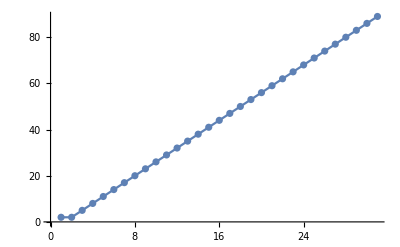

ListPlot::nonopt: Options expected (instead of Mesh→All) beyond position 1 in ListPlot[«1»]. An option must be a rule or a list of rules.

Show::gtype: ListPlot is not a type of graphics.

```mathematica
plt3=GraphSequence[func1, 0, 30];
Show[plt3]
```

```mathematica
fSum[n_]:=fSum[n]=(func1[n]*3-func1[1])/2
```

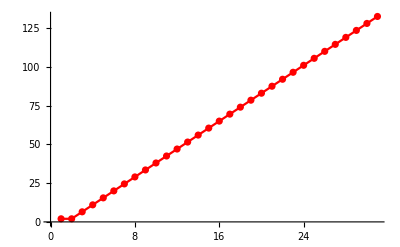

```mathematica
plt4=GraphSequence[fSum,0, 30, Red]
```

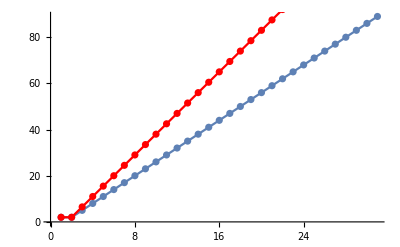

```mathematica
Show[plt3, plt4]
```

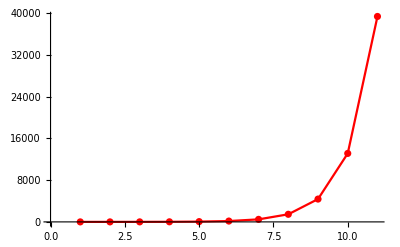

```mathematica
fGeom3[n_]:=fGeom3[n]=2*3^(n-1)
plt5=GraphSequence[fGeom3, 0, 10, Red]
```

```mathematica
fSum2[n_]:=fSum2[n]=2*(1-3^(n-1))/(1-3)
```

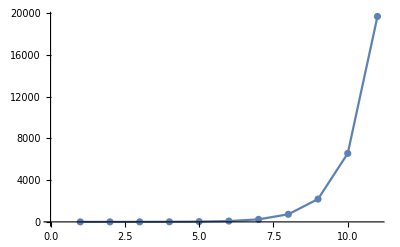

```mathematica
plt6=GraphSequence[fSum2, 0, 10]
```

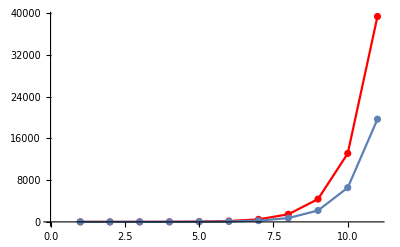

```mathematica
Show[plt5, plt6]
```

```mathematica
fUnc2[n_]:=fUnc2[n]=GCD[n,6]
```

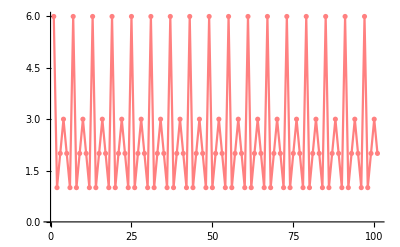

```mathematica
plt8=GraphSequence[fUnc2, 0, 100, Pink]
```

```mathematica
func3[n_]:=n^2*Mod[n,5]
```

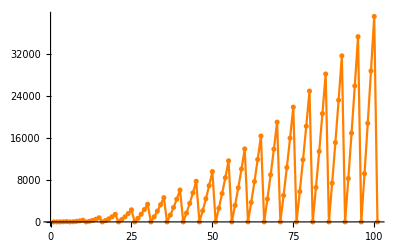

```mathematica
plt9=GraphSequence[func3, 0, 100, Orange]
```

```mathematica
func4[n_]:=func4[n]=Prime[n]
```

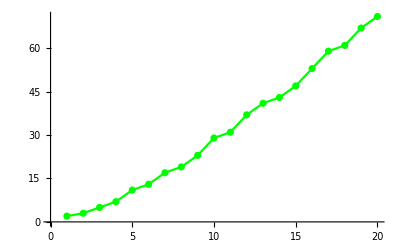

```mathematica
plt10=GraphSequence[func4, 1, 20, Green]
```

```mathematica
a
a={a1, a2, a3}
```

a

{a1,a2,a3}

```mathematica
Norm[a]
```

√(Abs[a1]^2+Abs[a2]^2+Abs[a3]^2)

```mathematica
Norm[a,1]
```

Abs[a1]+Abs[a2]+Abs[a3]

```mathematica
Norm[a, Infinity]
```

```mathematica
Max[Abs[a1],Abs[a2],Abs[a3]]
Norm[a, "Frobenius"]
```

Max[Abs[a1],Abs[a2],Abs[a3]]

√(Abs[a1]^2+Abs[a2]^2+Abs[a3]^2)

```mathematica
b={{a1, a2, a3},{a4, a5, a6},{a7, a8, a9}}
```

{{a1,a2,a3},{a4,a5,a6},{a7,a8,a9}}

```mathematica
%//MatrixForm
```

(a1 | a2 | a3
a4 | a5 | a6
a7 | a8 | a9)

```mathematica
Norm[b]
```

Max[√Root[-a3 a5 a7 Conjugate[a3] Conjugate[a5] Conjugate[a7]+a2 a6 a7 Conjugate[a3] Conjugate[a5] Conjugate[a7]+a3 a4 a8 Conjugate[a3] Conjugate[a5] Conjugate[a7]-a1 a6 a8 Conjugate[a3] Conjugate[a5] Conjugate[a7]-a2 a4 a9 Conjugate[a3] Conjugate[a5] Conjugate[a7]+a1 a5 a9 Conjugate[a3] Conjugate[a5] Conjugate[a7]+a3 a5 a7 Conjugate[a2] Conjugate[a6] Conjugate[a7]-a2 a6 a7 Conjugate[a2] Conjugate[a6] Conjugate[a7]-a3 a4 a8 Conjugate[a2] Conjugate[a6] Conjugate[a7]+a1 a6 a8 Conjugate[a2] Conjugate[a6] Conjugate[a7]+a2 a4 a9 Conjugate[a2] Conjugate[a6] Conjugate[a7]-a1 a5 a9 Conjugate[a2] Conjugate[a6] Conjugate[a7]+a3 a5 a7 Conjugate[a3] Conjugate[a4] Conjugate[a8]-a2 a6 a7 Conjugate[a3] Conjugate[a4] Conjugate[a8]-a3 a4 a8 Conjugate[a3] Conjugate[a4] Conjugate[a8]+a1 a6 a8 Conjugate[a3] Conjugate[a4] Conjugate[a8]+a2 a4 a9 Conjugate[a3] Conjugate[a4] Conjugate[a8]-a1 a5 a9 Conjugate[a3] Conjugate[a4] Conjugate[a8]-a3 a5 a7 Conjugate[a1] Conjugate[a6] Conjugate[a8]+a2 a6 a7 Conjugate[a1] Conjugate[a6] Conjugate[a8]+a3 a4 a8 Conjugate[a1] Conjugate[a6] Conjugate[a8]-a1 a6 a8 Conjugate[a1] Conjugate[a6] Conjugate[a8]-a2 a4 a9 Conjugate[a1] Conjugate[a6] Conjugate[a8]+a1 a5 a9 Conjugate[a1] Conjugate[a6] Conjugate[a8]-a3 a5 a7 Conjugate[a2] Conjugate[a4] Conjugate[a9]+a2 a6 a7 Conjugate[a2] Conjugate[a4] Conjugate[a9]+a3 a4 a8 Conjugate[a2] Conjugate[a4] Conjugate[a9]-a1 a6 a8 Conjugate[a2] Conjugate[a4] Conjugate[a9]-a2 a4 a9 Conjugate[a2] Conjugate[a4] Conjugate[a9]+a1 a5 a9 Conjugate[a2] Conjugate[a4] Conjugate[a9]+a3 a5 a7 Conjugate[a1] Conjugate[a5] Conjugate[a9]-a2 a6 a7 Conjugate[a1] Conjugate[a5] Conjugate[a9]-a3 a4 a8 Conjugate[a1] Conjugate[a5] Conjugate[a9]+a1 a6 a8 Conjugate[a1] Conjugate[a5] Conjugate[a9]+a2 a4 a9 Conjugate[a1] Conjugate[a5] Conjugate[a9]-a1 a5 a9 Conjugate[a1] Conjugate[a5] Conjugate[a9]+(a2 a4 Conjugate[a2] Conjugate[a4]-a1 a5 Conjugate[a2] Conjugate[a4]+a3 a4 Conjugate[a3] Conjugate[a4]-a1 a6 Conjugate[a3] Conjugate[a4]-a2 a4 Conjugate[a1] Conjugate[a5]+a1 a5 Conjugate[a1] Conjugate[a5]+a3 a5 Conjugate[a3] Conjugate[a5]-a2 a6 Conjugate[a3] Conjugate[a5]-a3 a4 Conjugate[a1] Conjugate[a6]+a1 a6 Conjugate[a1] Conjugate[a6]-a3 a5 Conjugate[a2] Conjugate[a6]+a2 a6 Conjugate[a2] Conjugate[a6]+a2 a7 Conjugate[a2] Conjugate[a7]-a1 a8 Conjugate[a2] Conjugate[a7]+a3 a7 Conjugate[a3] Conjugate[a7]-a1 a9 Conjugate[a3] Conjugate[a7]+a5 a7 Conjugate[a5] Conjugate[a7]-a4 a8 Conjugate[a5] Conjugate[a7]+a6 a7 Conjugate[a6] Conjugate[a7]-a4 a9 Conjugate[a6] Conjugate[a7]-a2 a7 Conjugate[a1] Conjugate[a8]+a1 a8 Conjugate[a1] Conjugate[a8]+a3 a8 Conjugate[a3] Conjugate[a8]-a2 a9 Conjugate[a3] Conjugate[a8]-a5 a7 Conjugate[a4] Conjugate[a8]+a4 a8 Conjugate[a4] Conjugate[a8]+a6 a8 Conjugate[a6] Conjugate[a8]-a5 a9 Conjugate[a6] Conjugate[a8]-a3 a7 Conjugate[a1] Conjugate[a9]+a1 a9 Conjugate[a1] Conjugate[a9]-a3 a8 Conjugate[a2] Conjugate[a9]+a2 a9 Conjugate[a2] Conjugate[a9]-a6 a7 Conjugate[a4] Conjugate[a9]+a4 a9 Conjugate[a4] Conjugate[a9]-a6 a8 Conjugate[a5] Conjugate[a9]+a5 a9 Conjugate[a5] Conjugate[a9]) #1+(-a1 Conjugate[a1]-a2 Conjugate[a2]-a3 Conjugate[a3]-a4 Conjugate[a4]-a5 Conjugate[a5]-a6 Conjugate[a6]-a7 Conjugate[a7]-a8 Conjugate[a8]-a9 Conjugate[a9]) #1^2+#1^3&,1],√Root[-a3 a5 a7 Conjugate[a3] Conjugate[a5] Conjugate[a7]+a2 a6 a7 Conjugate[a3] Conjugate[a5] Conjugate[a7]+a3 a4 a8 Conjugate[a3] Conjugate[a5] Conjugate[a7]-a1 a6 a8 Conjugate[a3] Conjugate[a5] Conjugate[a7]-a2 a4 a9 Conjugate[a3] Conjugate[a5] Conjugate[a7]+a1 a5 a9 Conjugate[a3] Conjugate[a5] Conjugate[a7]+a3 a5 a7 Conjugate[a2] Conjugate[a6] Conjugate[a7]-a2 a6 a7 Conjugate[a2] Conjugate[a6] Conjugate[a7]-a3 a4 a8 Conjugate[a2] Conjugate[a6] Conjugate[a7]+a1 a6 a8 Conjugate[a2] Conjugate[a6] Conjugate[a7]+a2 a4 a9 Conjugate[a2] Conjugate[a6] Conjugate[a7]-a1 a5 a9 Conjugate[a2] Conjugate[a6] Conjugate[a7]+a3 a5 a7 Conjugate[a3] Conjugate[a4] Conjugate[a8]-a2 a6 a7 Conjugate[a3] Conjugate[a4] Conjugate[a8]-a3 a4 a8 Conjugate[a3] Conjugate[a4] Conjugate[a8]+a1 a6 a8 Conjugate[a3] Conjugate[a4] Conjugate[a8]+a2 a4 a9 Conjugate[a3] Conjugate[a4] Conjugate[a8]-a1 a5 a9 Conjugate[a3] Conjugate[a4] Conjugate[a8]-a3 a5 a7 Conjugate[a1] Conjugate[a6] Conjugate[a8]+a2 a6 a7 Conjugate[a1] Conjugate[a6] Conjugate[a8]+a3 a4 a8 Conjugate[a1] Conjugate[a6] Conjugate[a8]-a1 a6 a8 Conjugate[a1] Conjugate[a6] Conjugate[a8]-a2 a4 a9 Conjugate[a1] Conjugate[a6] Conjugate[a8]+a1 a5 a9 Conjugate[a1] Conjugate[a6] Conjugate[a8]-a3 a5 a7 Conjugate[a2] Conjugate[a4] Conjugate[a9]+a2 a6 a7 Conjugate[a2] Conjugate[a4] Conjugate[a9]+a3 a4 a8 Conjugate[a2] Conjugate[a4] Conjugate[a9]-a1 a6 a8 Conjugate[a2] Conjugate[a4] Conjugate[a9]-a2 a4 a9 Conjugate[a2] Conjugate[a4] Conjugate[a9]+a1 a5 a9 Conjugate[a2] Conjugate[a4] Conjugate[a9]+a3 a5 a7 Conjugate[a1] Conjugate[a5] Conjugate[a9]-a2 a6 a7 Conjugate[a1] Conjugate[a5] Conjugate[a9]-a3 a4 a8 Conjugate[a1] Conjugate[a5] Conjugate[a9]+a1 a6 a8 Conjugate[a1] Conjugate[a5] Conjugate[a9]+a2 a4 a9 Conjugate[a1] Conjugate[a5] Conjugate[a9]-a1 a5 a9 Conjugate[a1] Conjugate[a5] Conjugate[a9]+(a2 a4 Conjugate[a2] Conjugate[a4]-a1 a5 Conjugate[a2] Conjugate[a4]+a3 a4 Conjugate[a3] Conjugate[a4]-a1 a6 Conjugate[a3] Conjugate[a4]-a2 a4 Conjugate[a1] Conjugate[a5]+a1 a5 Conjugate[a1] Conjugate[a5]+a3 a5 Conjugate[a3] Conjugate[a5]-a2 a6 Conjugate[a3] Conjugate[a5]-a3 a4 Conjugate[a1] Conjugate[a6]+a1 a6 Conjugate[a1] Conjugate[a6]-a3 a5 Conjugate[a2] Conjugate[a6]+a2 a6 Conjugate[a2] Conjugate[a6]+a2 a7 Conjugate[a2] Conjugate[a7]-a1 a8 Conjugate[a2] Conjugate[a7]+a3 a7 Conjugate[a3] Conjugate[a7]-a1 a9 Conjugate[a3] Conjugate[a7]+a5 a7 Conjugate[a5] Conjugate[a7]-a4 a8 Conjugate[a5] Conjugate[a7]+a6 a7 Conjugate[a6] Conjugate[a7]-a4 a9 Conjugate[a6] Conjugate[a7]-a2 a7 Conjugate[a1] Conjugate[a8]+a1 a8 Conjugate[a1] Conjugate[a8]+a3 a8 Conjugate[a3] Conjugate[a8]-a2 a9 Conjugate[a3] Conjugate[a8]-a5 a7 Conjugate[a4] Conjugate[a8]+a4 a8 Conjugate[a4] Conjugate[a8]+a6 a8 Conjugate[a6] Conjugate[a8]-a5 a9 Conjugate[a6] Conjugate[a8]-a3 a7 Conjugate[a1] Conjugate[a9]+a1 a9 Conjugate[a1] Conjugate[a9]-a3 a8 Conjugate[a2] Conjugate[a9]+a2 a9 Conjugate[a2] Conjugate[a9]-a6 a7 Conjugate[a4] Conjugate[a9]+a4 a9 Conjugate[a4] Conjugate[a9]-a6 a8 Conjugate[a5] Conjugate[a9]+a5 a9 Conjugate[a5] Conjugate[a9]) #1+(-a1 Conjugate[a1]-a2 Conjugate[a2]-a3 Conjugate[a3]-a4 Conjugate[a4]-a5 Conjugate[a5]-a6 Conjugate[a6]-a7 Conjugate[a7]-a8 Conjugate[a8]-a9 Conjugate[a9]) #1^2+#1^3&,2],√Root[-a3 a5 a7 Conjugate[a3] Conjugate[a5] Conjugate[a7]+a2 a6 a7 Conjugate[a3] Conjugate[a5] Conjugate[a7]+a3 a4 a8 Conjugate[a3] Conjugate[a5] Conjugate[a7]-a1 a6 a8 Conjugate[a3] Conjugate[a5] Conjugate[a7]-a2 a4 a9 Conjugate[a3] Conjugate[a5] Conjugate[a7]+a1 a5 a9 Conjugate[a3] Conjugate[a5] Conjugate[a7]+a3 a5 a7 Conjugate[a2] Conjugate[a6] Conjugate[a7]-a2 a6 a7 Conjugate[a2] Conjugate[a6] Conjugate[a7]-a3 a4 a8 Conjugate[a2] Conjugate[a6] Conjugate[a7]+a1 a6 a8 Conjugate[a2] Conjugate[a6] Conjugate[a7]+a2 a4 a9 Conjugate[a2] Conjugate[a6] Conjugate[a7]-a1 a5 a9 Conjugate[a2] Conjugate[a6] Conjugate[a7]+a3 a5 a7 Conjugate[a3] Conjugate[a4] Conjugate[a8]-a2 a6 a7 Conjugate[a3] Conjugate[a4] Conjugate[a8]-a3 a4 a8 Conjugate[a3] Conjugate[a4] Conjugate[a8]+a1 a6 a8 Conjugate[a3] Conjugate[a4] Conjugate[a8]+a2 a4 a9 Conjugate[a3] Conjugate[a4] Conjugate[a8]-a1 a5 a9 Conjugate[a3] Conjugate[a4] Conjugate[a8]-a3 a5 a7 Conjugate[a1] Conjugate[a6] Conjugate[a8]+a2 a6 a7 Conjugate[a1] Conjugate[a6] Conjugate[a8]+a3 a4 a8 Conjugate[a1] Conjugate[a6] Conjugate[a8]-a1 a6 a8 Conjugate[a1] Conjugate[a6] Conjugate[a8]-a2 a4 a9 Conjugate[a1] Conjugate[a6] Conjugate[a8]+a1 a5 a9 Conjugate[a1] Conjugate[a6] Conjugate[a8]-a3 a5 a7 Conjugate[a2] Conjugate[a4] Conjugate[a9]+a2 a6 a7 Conjugate[a2] Conjugate[a4] Conjugate[a9]+a3 a4 a8 Conjugate[a2] Conjugate[a4] Conjugate[a9]-a1 a6 a8 Conjugate[a2] Conjugate[a4] Conjugate[a9]-a2 a4 a9 Conjugate[a2] Conjugate[a4] Conjugate[a9]+a1 a5 a9 Conjugate[a2] Conjugate[a4] Conjugate[a9]+a3 a5 a7 Conjugate[a1] Conjugate[a5] Conjugate[a9]-a2 a6 a7 Conjugate[a1] Conjugate[a5] Conjugate[a9]-a3 a4 a8 Conjugate[a1] Conjugate[a5] Conjugate[a9]+a1 a6 a8 Conjugate[a1] Conjugate[a5] Conjugate[a9]+a2 a4 a9 Conjugate[a1] Conjugate[a5] Conjugate[a9]-a1 a5 a9 Conjugate[a1] Conjugate[a5] Conjugate[a9]+(a2 a4 Conjugate[a2] Conjugate[a4]-a1 a5 Conjugate[a2] Conjugate[a4]+a3 a4 Conjugate[a3] Conjugate[a4]-a1 a6 Conjugate[a3] Conjugate[a4]-a2 a4 Conjugate[a1] Conjugate[a5]+a1 a5 Conjugate[a1] Conjugate[a5]+a3 a5 Conjugate[a3] Conjugate[a5]-a2 a6 Conjugate[a3] Conjugate[a5]-a3 a4 Conjugate[a1] Conjugate[a6]+a1 a6 Conjugate[a1] Conjugate[a6]-a3 a5 Conjugate[a2] Conjugate[a6]+a2 a6 Conjugate[a2] Conjugate[a6]+a2 a7 Conjugate[a2] Conjugate[a7]-a1 a8 Conjugate[a2] Conjugate[a7]+a3 a7 Conjugate[a3] Conjugate[a7]-a1 a9 Conjugate[a3] Conjugate[a7]+a5 a7 Conjugate[a5] Conjugate[a7]-a4 a8 Conjugate[a5] Conjugate[a7]+a6 a7 Conjugate[a6] Conjugate[a7]-a4 a9 Conjugate[a6] Conjugate[a7]-a2 a7 Conjugate[a1] Conjugate[a8]+a1 a8 Conjugate[a1] Conjugate[a8]+a3 a8 Conjugate[a3] Conjugate[a8]-a2 a9 Conjugate[a3] Conjugate[a8]-a5 a7 Conjugate[a4] Conjugate[a8]+a4 a8 Conjugate[a4] Conjugate[a8]+a6 a8 Conjugate[a6] Conjugate[a8]-a5 a9 Conjugate[a6] Conjugate[a8]-a3 a7 Conjugate[a1] Conjugate[a9]+a1 a9 Conjugate[a1] Conjugate[a9]-a3 a8 Conjugate[a2] Conjugate[a9]+a2 a9 Conjugate[a2] Conjugate[a9]-a6 a7 Conjugate[a4] Conjugate[a9]+a4 a9 Conjugate[a4] Conjugate[a9]-a6 a8 Conjugate[a5] Conjugate[a9]+a5 a9 Conjugate[a5] Conjugate[a9]) #1+(-a1 Conjugate[a1]-a2 Conjugate[a2]-a3 Conjugate[a3]-a4 Conjugate[a4]-a5 Conjugate[a5]-a6 Conjugate[a6]-a7 Conjugate[a7]-a8 Conjugate[a8]-a9 Conjugate[a9]) #1^2+#1^3&,3]]

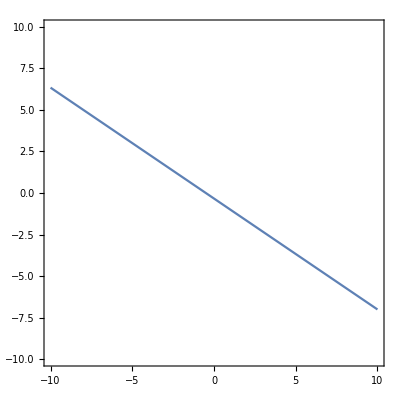

```mathematica
ContourPlot[2x+3y+1==0,{x, -10, 10}, {y, -10, 10}]
```

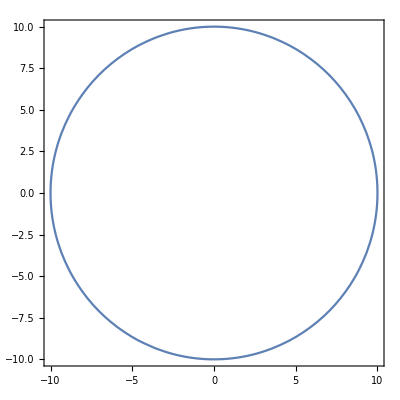

```mathematica
ContourPlot[x^2+y^2==100, {x, -10, 10}, {y, -10, 10}]
```

```mathematica
Manipulate[ContourPlot[a1*x^2+a2*x*y+a3*y^2+a4*x+a5*y+a6==0, {x, -20, 20}, {y, -20, 20} ],{a1, -10, 10},{a2, -10, 10},{a3, -10, 10},{a4, -10, 10},{a5, -10, 10},{a6, -10, 10}, Axes->True]
```

```mathematica
Manipulate[ContourPlot3D[a1*x^2+a2*y^2+a3*z^2+a4*x*y+a5*y*z+a6*x*z+a7*x+a8*y+a9*z+a10==0, {x, -20, 20}, {y, -20, 20} ,{z, -20,20}],{a1, -10, 10},{a2, -10, 10},{a3, -10, 10},{a4, -10, 10},{a5, -10, 10},{a6, -10, 10},{a7, -10,10}, {a8, -10, 10},{a9, -10, 10}, {a10, -10, 10},Axes->True]
```

```mathematica
Ynew[x_]:=Sqrt[1-Exp[-3*x^2]]
```

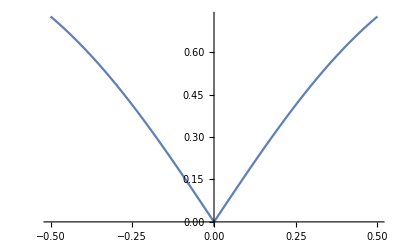

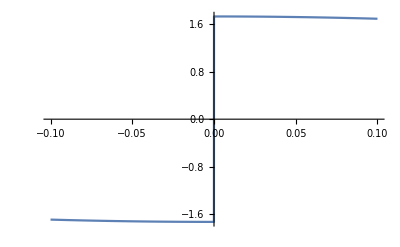

```mathematica
Plot[Ynew[x], {x,-0.5,0.5}]
Plot[Ynew'[x], {x,-0.1,0.1}]
```

```mathematica
GraphSequence[formula_,min_, max_, color_:Blue]:=ListPlot[Table[formula[i],{i, min, max}],Joined->True,Mesh->All, PlotStyle->color]
```

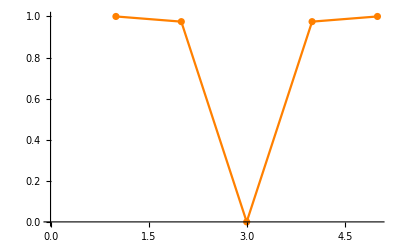

```mathematica
plt100=GraphSequence[Ynew,-2, 2, Orange]
```

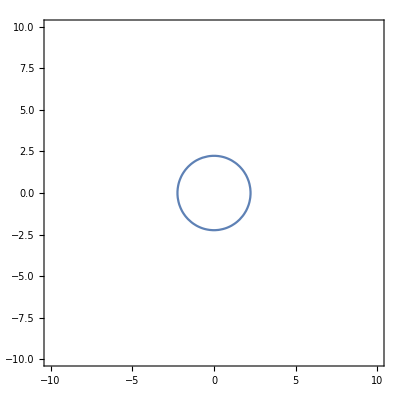

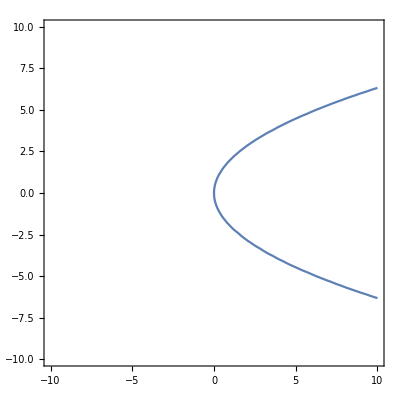

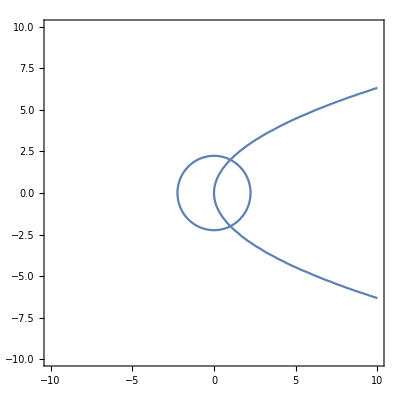

```mathematica
ContourPlot[x^2+y^2==5, {x,-10,10}, {y,-10,10},Axes->True]
ContourPlot[y^2==4x,{x,-10,10}, {y,-10,10},Axes->True]
Show[ContourPlot[x^2+y^2==5, {x,-10,10}, {y,-10,10},Axes->True],ContourPlot[y^2==4x,{x,-10,10}, {y,-10,10},Axes->True]]
```